```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Covariance[MultivariateTDistribution[{5,5},{{σ1^2,ρ σ1 σ2},{ρ σ1 σ2,σ2^2}},ν]]
```

Piecewise[{{{{(ν σ1^2)/(-2+ν),(ν ρ σ1 σ2)/(-2+ν)},{(ν ρ σ1 σ2)/(-2+ν),(ν σ2^2)/(-2+ν)}}, ν>2}, {Indeterminate, True}}]

```mathematica
customMultivariateT[mu_,aSigma_,ν_]:=Module[{aSigmaAdjusted = aSigma * ((ν-2)/ν)},MultivariateTDistribution[mu,aSigmaAdjusted,ν]]
```

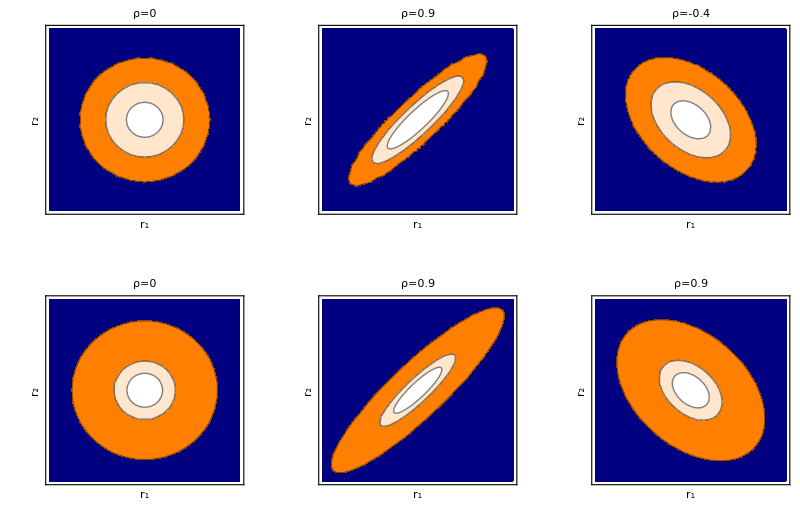

```mathematica
Subscript[σ, 11] = 1;
Subscript[σ, 22]= 1;
ρ1 = 0;
Σ1={{Subscript[σ, 11]^2,ρ1 Subscript[σ, 11] Subscript[σ, 22]},{ρ1 Subscript[σ, 11] Subscript[σ, 22],Subscript[σ, 22]^2}};
Subscript[σ, 11] = 1;
Subscript[σ, 22]= 1;
ρ2 = 0.9;
Σ2={{Subscript[σ, 11]^2,ρ2 Subscript[σ, 11] Subscript[σ, 22]},{ρ2 Subscript[σ, 11] Subscript[σ, 22],Subscript[σ, 22]^2}};
Subscript[σ, 11] =1;
Subscript[σ, 22]= 1;
ρ3 = -0.4;
Σ3={{Subscript[σ, 11]^2,ρ3 Subscript[σ, 11] Subscript[σ, 22]},{ρ3 Subscript[σ, 11] Subscript[σ, 22],Subscript[σ, 22]^2}};
a1 = 0.1;
a2 = 0.02;
a3 = 0.0005;
aContour ={a3,a2,a1};
aContourLabels = False;
fColourFunction[aNum_]:=(If[aNum>a1,White,If[aNum>a2,LightOrange,If[aNum>a3,Orange,Darker[Blue,0.5]]]])
g1=ContourPlot[PDF[MultinormalDistribution[{5,5},Σ1],{x,y}],{x,0,10},{y,0,10},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"r_1","r_2"},BaseStyle->{FontSize->18},FrameTicks->{None,None},PlotLabel->StringJoin["ρ=",ToString[ρ1]],Contours->aContour,ColorFunction->(fColourFunction[#]&),ContourLabels->aContourLabels,ColorFunctionScaling->False];
g2=ContourPlot[PDF[MultinormalDistribution[{5,5},Σ2],{x,y}],{x,0,10},{y,0,10},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"r_1","r_2"},BaseStyle->{FontSize->18},FrameTicks->{None,None},PlotLabel->StringJoin["ρ=",ToString[ρ2]],Contours->aContour,ColorFunction->(fColourFunction[#]&),ContourLabels->aContourLabels,ColorFunctionScaling->False];
g3=ContourPlot[PDF[MultinormalDistribution[{5,5},Σ3],{x,y}],{x,0,10},{y,0,10},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"r_1","r_2"},BaseStyle->{FontSize->18},FrameTicks->{None,None},PlotLabel->StringJoin["ρ=",ToString[ρ3]],Contours->aContour,ColorFunction->(fColourFunction[#]&),ContourLabels->aContourLabels,ColorFunctionScaling->False];
g1T=ContourPlot[PDF[customMultivariateT[{5,5},Σ1,3],{x,y}],{x,0,10},{y,0,10},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"r_1","r_2"},BaseStyle->{FontSize->18},FrameTicks->{None,None},PlotLabel->StringJoin["ρ=",ToString[ρ1]],Contours->aContour,ColorFunction->(fColourFunction[#]&),ContourLabels->aContourLabels,ColorFunctionScaling->False];
g2T=ContourPlot[PDF[customMultivariateT[{5,5},Σ2,3],{x,y}],{x,0,10},{y,0,10},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"r_1","r_2"},BaseStyle->{FontSize->18},FrameTicks->{None,None},PlotLabel->StringJoin["ρ=",ToString[ρ2]],Contours->aContour,ColorFunction->(fColourFunction[#]&),ContourLabels->aContourLabels,ColorFunctionScaling->False];
g3T=ContourPlot[PDF[customMultivariateT[{5,5},Σ3,3],{x,y}],{x,0,10},{y,0,10},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"r_1","r_2"},BaseStyle->{FontSize->18},FrameTicks->{None,None},PlotLabel->StringJoin["ρ=",ToString[ρ2]],Contours->aContour,ColorFunction->(fColourFunction[#]&),ContourLabels->aContourLabels,ColorFunctionScaling->False];
gFinal=Show[GraphicsGrid[{{g1,g2,g3},{g1T,g2T,g3T}}],ImageSize->800]
```

```mathematica
Export["Distributions_multivariateNormalT.pdf",gFinal]
```

Distributions_multivariateNormalT.pdf